Chapter 6, Section 6.3 “MB Numerical Evaluation by Steepest Descent”

Results below are connected with Fig.6.6 and the note on “MBDE solutions in Euclidean and Minkowskian kinematics”

```mathematica
(* f1 = (-s)^(-z)(Gamma[-z]^3Gamma[1+z])/Gamma[-2z] *)
```

```mathematica
SetOptions[Plot,Frame->True,AspectRatio->1,Axes-> False,PlotRange-> All];
```

```mathematica
SetOptions[ContourPlot,Frame->True,AspectRatio->1,Axes-> False];
```

```mathematica
SetOptions[ParametricPlot,Frame->True,AspectRatio->1,Axes-> False];
```

```mathematica
t1=AbsoluteTime[];
```

```mathematica
s0=SetPrecision[1+I*10^(-11),40];
```

```mathematica
Fint=-Log[(-s)^(-z) (Gamma[-z]^3Gamma[1+z])/Gamma[-2z]]//FullSimplify;
```

```mathematica
DFint=D[Fint,z]//FullSimplify
```

EulerGamma-HarmonicNumber[z]+Log[-s]-2 PolyGamma[0,-2 z]+3 PolyGamma[0,-z]

```mathematica
conDF=Conjugate[DFint/.{z-> z[t]}]
```

EulerGamma-Conjugate[HarmonicNumber[z[t]]]+Conjugate[Log[-s]]-2 Conjugate[PolyGamma[0,-2 z[t]]]+3 Conjugate[PolyGamma[0,-z[t]]]

```mathematica
dF=DFint/.{z-> x[t]+I*y[t]}
```

EulerGamma-HarmonicNumber[x[t]+ⅈ y[t]]+Log[-s]+3 PolyGamma[0,-x[t]-ⅈ y[t]]-2 PolyGamma[0,-2 (x[t]+ⅈ y[t])]

```mathematica
dbFb=DFint/.{z-> x[t]-I*y[t]}
```

EulerGamma-HarmonicNumber[x[t]-ⅈ y[t]]+Log[-s]-2 PolyGamma[0,-2 (x[t]-ⅈ y[t])]+3 PolyGamma[0,-x[t]+ⅈ y[t]]

```mathematica
FindRoot[DFint/.{s->s0},{z,-0.7},WorkingPrecision->40]
```

{z→-0.7893196678488500697745302204512988472233-0.1745322927594659311248130718362495660459 ⅈ}

```mathematica
%[[1,2]]
```

-0.7893196678488500697745302204512988472233-0.1745322927594659311248130718362495660459 ⅈ

```mathematica
zsad=z/.FindRoot[DFint/.{s->s0},{z,-0.7},WorkingPrecision->40]
```

-0.7893196678488500697745302204512988472233-0.1745322927594659311248130718362495660459 ⅈ

```mathematica
(* cross-check if x'[0]=y'[0]=0 *)
```

```mathematica
{(dbFb+dF),(dbFb-dF)}/.{s->s0}/.{t-> 0}/.{x[0]->Re[zsad],y[0]-> Im[zsad]}//FullSimplify
```

{0.-6.283185307159586476925286766559006435061 ⅈ,0.-6.283185307159586476925286766559006435061 ⅈ}

```mathematica
ImFval=SetPrecision[Im[Fint]/.{s->s0}/.{z-> Re[zsad]+I*Im[zsad]},40]
```

2.289999460931087118990742901382121591459

```mathematica
poles=Table[{i,0},{i,-30,30}];
```

```mathematica
conORG=ContourPlot[{(Im[Fint]/.{s->s0}/.{z-> x+I*y})==ImFval,x==-1/2},{x,-5,1},{y,-1,4},PlotPoints->100,Epilog-> {{Red,Point[poles]},{Black,Point[{{Re[zsad],Im[zsad]}}]}}];
```

```mathematica
D2f=SetPrecision[{{D[(Fint/.{s->s0}/.{z-> x+I*y}),x,x],D[(Fint/.{s->s0}/.z-> x+I*y),x,y]},{D[(Fint/.{s->s0}/.z-> x+I*y),y,x],D[(Fint/.{s->s0}/.z-> x+I*y),y,y]}}/.{x->Re[zsad],y-> Im[zsad]},40];
```

```mathematica
v1=SetPrecision[-Eigenvectors[Re[D2f]][[2]],40];
```

```mathematica
v2=SetPrecision[-Eigenvectors[Re[D2f]][[1]],40];
```

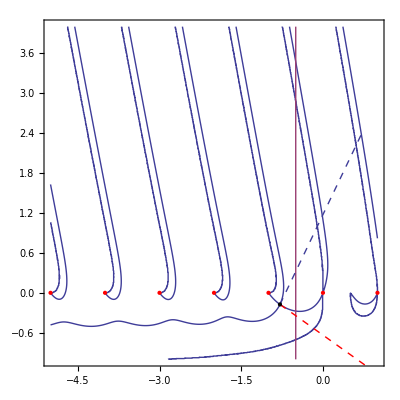

```mathematica
Show[conORG,ParametricPlot[{{Re[zsad]+t*v1[[1]],Im[zsad]+t*v1[[2]]},{Re[zsad]+t*v2[[1]],Im[zsad]+t*v2[[2]]}},{t,0,3},PlotStyle-> {Dashed,Directive[Red,Dashed]}]]
```

```mathematica
t0in=SetPrecision[10^(-12),40];
```

```mathematica
solPAR1=NDSolve[{z'[t]==SetPrecision[conDF/.{s->s0},40],{z[0]==zsad+t0*(v1[[1]]+I*v1[[2]])/.{t0-> t0in}}},z,{t,0,20},WorkingPrecision->40,MaxStepSize->10^(-3),MaxSteps-> Infinity][[1]];
```

```mathematica
solPAR2=NDSolve[{z'[t]==SetPrecision[conDF/.{s->s0},40],{z[0]==zsad+t0*(v1[[1]]+I*v1[[2]])/.{t0-> -t0in}}},z,{t,0,20},WorkingPrecision->40,MaxStepSize->10^(-3),MaxSteps-> Infinity][[1]];
```

```mathematica
conPAR=ParametricPlot[{Evaluate[{Re[z[t]],Im[z[t]]}/.solPAR1],Evaluate[{Re[z[t]],Im[z[t]]}/.solPAR2],{Re[zsad+I*t*Exp[I*(-0.528899)]+t^2*(-0.931716+0.575462*I)],Im[zsad+I*t*Exp[I*(-0.528899)]+t^2*(-0.931716+0.575462*I)]},{Re[zsad-I*t*Exp[I*(-0.528899)]+t^2*(-0.931716+0.575462*I)],Im[zsad-I*t*Exp[I*(-0.528899)]+t^2*(-0.931716+0.575462*I)]}},{t,0,10},PlotStyle->{Directive[Black,Thickness[0.005]],Directive[Black,Thickness[0.005]],Directive[Orange,Dashed,Thickness[0.005]],Directive[Orange,Dashed,Thickness[0.005]]},Axes-> False,PlotRange->{{-10,0},{-2,5}}];
```

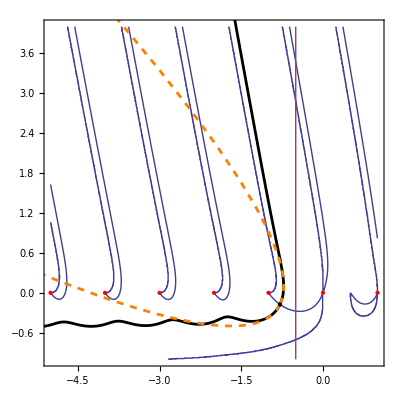

```mathematica
Show[conORG,conPAR]
```

```mathematica
int1=1/(2Pi I)NIntegrate[Evaluate[conDF Exp[-Fint/.{z-> z[t]}]/.{s->s0}/.solPAR1],{t,0,30},WorkingPrecision->40,PrecisionGoal->12,MaxRecursion->10^3];
```

```mathematica
int2=1/(2Pi I)NIntegrate[Evaluate[conDF Exp[-Fint/.{z-> z[t]}]/.{s->s0}/.solPAR2],{t,0,30},WorkingPrecision->40,PrecisionGoal->12,MinRecursion->10^4,MaxRecursion->10^5];
```

```mathematica
intf1=int1-int2
```

-1.209199576127040229046351045612544212205-1.5476755760777198668163169699×10^-11 ⅈ

```mathematica
(* analytical value of the integral *)
```

```mathematica
intf1an=(-1)4/Sqrt[4/s-1] ArcSin[Sqrt[s/4]]/.{s->s0}
```

-1.20919957615614523372935217176143715486-1.47279971743743015581958138×10^-11 ⅈ

```mathematica
(* accuracy *)
```

```mathematica
Abs[1-Abs[Re[intf1]/Re[intf1an]]]
```

2.406964512468764360955749173×10^-11

```mathematica
AbsoluteTime[]-t1
```

336.39062